# Galaxy redshift

## Programming techniques

## Doppler shift

### Typed from student sheet

```mathematica
c=343.;dx=50;f0=300;v0=100;
source[x_,t_]:=Exp[-(x+c t)^2/dx^2] Cos[2 π f0(t+x/c)]
xp[t_]:=v0 t;
s=5000;dt=1/s;T=1;
ts=Table[source[xp[t],t],{t,-T/2,T/2,dt}];
```

### Answers to questions

-Graphics-

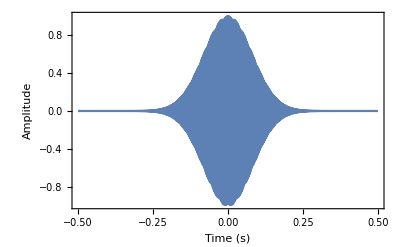

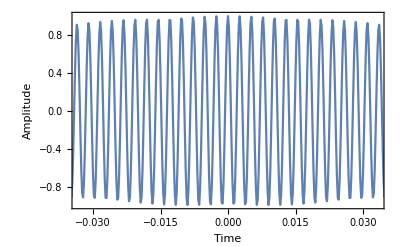

```mathematica
ListLinePlot[ts,PlotRange->All,Frame->True,DataRange->{-T/2,T/2},FrameLabel->{"Time (s)","Amplitude"}]

ListLinePlot[ts,PlotRange->{{-10/f0,10/f0},All},DataRange->{-T/2,T/2},Frame->True,FrameLabel->{"Time","Amplitude"}]
```

-Graphics-

Find the position (in list item index) or the peaks

```mathematica
peaks=FindPeaks[ts];
```

-Graphics-

Differences calculates the difference between successive values in the list. So here it is the index difference between peaks. We multiply this average difference by the known separation of the lists elements, dt, to get the average time-separation of the peaks.

```mathematica
period=dt peaks[[All,1]]//Differences//N//Mean
1/period
fd=f0 +v0/c f0
(* ListPlay[ts,SampleRate->s,PlayRange->All] *)
```

0.00257732

388.

387.464

-Graphics-

Here we iterate through the list ts, looking for when the product of two neighbouring  elements is negative. When this happens we know that one must be positive and the other negative, so we have crossed the x-axis. We then also check if the second element (position i, as opposed to position i-1) is positive. If this is the case then we know that we have crossed the x-axis, and that the signal is rising. We store this position in our new list if the conditions are met, otherwise we store an easily removed dummy-marker. Missing is easily removed from a list by DeleteMissing, just leaving a list of the rising x-axis crossing position. Notice that the If condition here bears some resemblance to the WhenEvent condition used in the Celestial Mechanics period finding function *)

```mathematica
pos=Table[If[ts[[i]] ts[[i-1]]<0&&ts[[i]]>0,i,Missing[]],{i,2,Length[ts]}];
period=dt Mean[Differences[N[DeleteMissing[pos]]]]
1/period
```

0.00258083

387.472

## Importing ASCII data and fitting

### Typed from student sheet

```mathematica
path="https://www.st-andrews.ac.uk/~ph3080/";
rawdata=Import[path<>"galaxies/spectrum.dat"];
rawdata[[1;;2]]//TableForm
dat=rawdata[[3;;-1]];
```

Frequency | Voltage
Hz | V

### Answers to questions

-Graphics-

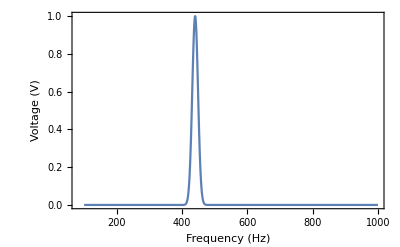

```mathematica
ListLinePlot[dat,PlotRange->All, Frame->True,FrameLabel->{"Frequency (Hz)", "Voltage (V)"}]
```

-Graphics-

```mathematica
index=FindPeaks[dat[[All,2]],0,0,0.5][[1,1]]//Round;
freq0=dat[[index,1]]
```

440

-Graphics-

```mathematica
Clear[fd]; (* used earlier *)
model=a Exp[-(fr-fd)^2/ω^2];
fit=FindFit[dat,model,{a,{fd,freq0},ω},fr]
```

{a→1.,fd→440.,ω→12.5}

-Graphics-

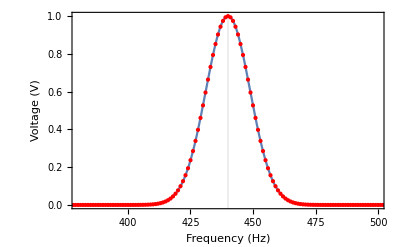

```mathematica
model=a Exp[-(fr-fd)^2/ω^2];
Plot[model/.fit,{fr,380,500},PlotRange->All,Frame->True,FrameLabel->{"Frequency (Hz)","Voltage (V)"},Epilog->{Red,Point[dat]},GridLines->{{fd}/.fit}]
```

## Importing multiple PNG files

### Typed from student sheet

```mathematica
path="https://www.st-andrews.ac.uk/~ph3080/";obswave=Table[w,{w,650.1,679.9,0.2}]; (* wavelength list in nm *)data=3.*10^-14Table[Import[path<>"case3/NGC7591/NGC7591."<>ToString[w]<>".png","Data"],{w,obswave}];
```

### Answers to questions

-Graphics-

```mathematica
Dimensions[data]
Dimensions[obswave]
```

{150,73,78}

{150}

Dimensions of data show a rectangle of 78*73 pixels (x,y) each with the flux of light at 150 wavelengths measured.

{150,73,78}

{150}

-Graphics-

```mathematica
ListDensityPlot3D[data  ,PlotLegends->Automatic,PlotLabel->"NGC7591, scaled energy flux densities, nW/(m^2 nm)",AxesLabel->{"x","y","Wavelength (nm)"},DataRange->{{1,78},{1,73},{650.1,679.9}},PlotRange->All]
```

-Graphics3D-

-Graphics-

The Total function totals at level 1 by default, so in this case it sums the flux of all wavelengths at each pixel.
The Image function expects values between 0-1, so saturates (like an overexposed photograph) and loses detail in our image if we don’t rescale the data into this range. By default, Rescale takes all the data an scales it into the range 0-1.

```mathematica
totintensity = Total[data];
Dimensions[totintensity] (*nice check on what data structure returned*)

Image[Rescale[totintensity],ImageSize->Medium]
```

{73,78}

-Graphics-

## Study

-Graphics-

### Total spectrum of whole galaxy

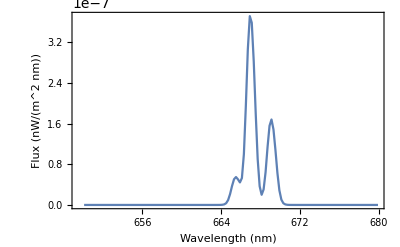

```mathematica
totspec =Transpose[ {obswave,Total[data,{2,3}]}];
(* Compare to spectrum in lecture slides to notice that we have Halpha+NII lines and OIII+Hb lines *)
ListLinePlot[totspec,PlotRange->All,Frame->True,FrameLabel->{{"Flux (nW/(m^2 nm))",""},{"Wavelength (nm)","NGC7591"}}]
```

-Graphics-

### Identify lines

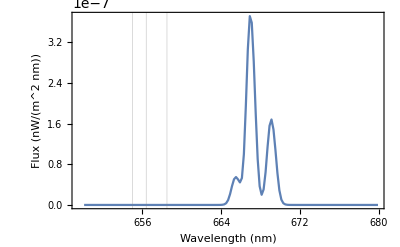

```mathematica
restpeaks={655.0,656.4,658.5};
ListLinePlot[totspec,PlotRange->All,Frame->True,GridLines->{restpeaks},FrameLabel->{{"Flux (nW/(m^2 nm))",""},{"Wavelength (nm)","NGC7591"}}]
```

-Graphics-

### Estimate redshift from FindPeaks

```mathematica
findex=FindPeaks[totspec[[All,2]],0,0,10^-9][[All,1]]
peaks=totspec[[findex,1]]
zs=(peaks-restpeaks)/restpeaks//Mean
```

{78,85,96}

{665.5,666.9,669.1}

0.0160414

-Graphics-

### Fit 3 Gaussians

{z→0.0161193,σ→0.58807,a[1]→5.30724×10^-8,a[2]→3.77171×10^-7,a[3]→1.71622×10^-7}

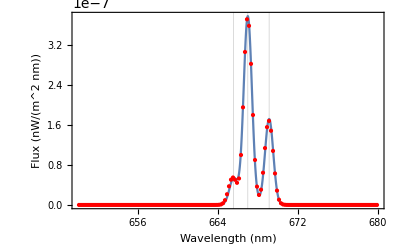

```mathematica
Off[General::munfl] (* This command switches off the warning messages concerning the numerical underflow. *)

specmodel=Sum[a[i] Exp[-(λ-(1+z)restpeaks[[i]])^2/σ^2],{i,Length[restpeaks]}];
vars=Join[{{z,zs},σ},Table[a[i],{i,Length[restpeaks]}]];
fit=FindFit[totspec,specmodel,vars,λ]

Plot[specmodel/.fit,{λ,650.0,680.0},Epilog->{Red,Point[totspec]},PlotRange->All,Frame->True,GridLines->{(1+z)restpeaks/.fit},FrameLabel->{{"Flux (nW/(m^2 nm))",""},{"Wavelength (nm)","NGC7591"}}]
```

-Graphics-

### Determine recession velocity and distance to galaxy

```mathematica
H0 = 67.7/3.09*^19; (* Hubble's constant in 1/s *)                       
c = 2.9979*10^8  ; (* speed of light in m/s *)
vr=z c /.fit 
distance=vr/H0
```

4.83242×10^6

2.20564×10^24

-Graphics-

### Line flux

```mathematica
lineFlux=NIntegrate[specmodel[[2]]/.fit,{λ,650,680}] (* nW/m^2 *)
```

3.93135×10^-7

-Graphics-

### Total energy irradiated by galaxy for Hα

```mathematica
4 π distance^2 lineFlux (* in nW *)
```

2.40337×10^43

-Graphics-

### Determine redshift in points (33,33) and (42,42)

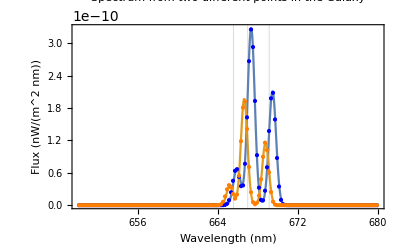

```mathematica
spec33 =Transpose[ {obswave,data[[All,33,33]]}];
spec42 =Transpose[ {obswave,data[[All,42,42]]}];
fit33=FindFit[spec33,specmodel,vars,λ];
fit42=FindFit[spec42,specmodel,vars,λ];

Plot[{specmodel/.fit33,specmodel/.fit42},{λ,650.0,680.0},Epilog->{Blue,Point[spec33],Orange,Point[spec42]},PlotRange->All,Frame->True,GridLines->{(1+z)restpeaks/.fit},FrameLabel->{{"Flux (nW/(m^2 nm))",""},{"Wavelength (nm)","NGC7591"}},
PlotLabel->"Spectrum from two different points in the Galaxy"]
```

-Graphics-

## Deduce the local velocities at these points

```mathematica
z c-vr/.fit33
z c-vr/.fit42
```

153646.

-164316.